## matrix-count_tests

Versions of the estimates to test, also validation on test cases that the moments indeed match

### Functions

```mathematica
logBinom[a_,b_]:=LogGamma[a+1]-LogGamma[b+1]-LogGamma[a-b+1]
```

```mathematica
firstMoment = t/n;
```

```mathematica
DMdistrbutionMeans[total_,length_,α_]:=Table[ total/length,{i,1,length}]
```

```mathematica
secondCentralMoment = t/n(n α + t)/(n α + 1)(d - n^(-1));
```

```mathematica
DMdistrbutionCovariances[total_,length_,α_]:=Table[ total/length(length α + total)/(length α + 1)(If[i==j,1,0]-length^(-1)),{i,1,length},{j,1,length}]
```

## Matrix generation

Explicitly generating all matrices within the simpler ensembles that we calculate moments over

### Useful functions

```mathematica
genAllVectorsGmn[m_,n_]:=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[m+n,{n}]-1,1]]
```

```mathematica
gen01VectorsGmn[m_,n_]:=Permutations[Join[ConstantArray[1,m],ConstantArray[0,n-m]]]
```

Convert a vector into a symmetric matrix

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
conFlatToMat[{a,b,c}]//MatrixForm
```

(2 a | b
b | 2 c)

vec populates the off diagonal, double the diag gives the diagonal:

```mathematica
conFlatToMatDiag[vec_,diag_]:=Module[{q,res,t},q =1/2 (1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i+1,q}],{i,1,q}];Do[res[[i,i]]=2*diag[[i]],{i,1,q}];
res]
```

```mathematica
conFlatToMatDiag[{a,b,c},{d,e,f}]//MatrixForm
```

(2 d | a | b
a | 2 e | c
b | c | 2 f)

### symmetric

#### binary_matrix = False, diagonal_sum = None

```mathematica
genAllMatsAllDiagGmn[m_,n_]:=Module[{nU,vecs},nU=n(n+1)/2;vecs=genAllVectorsGmn[m,nU];conFlatToMat/@vecs]
```

```mathematica
MatrixForm/@genAllMatsAllDiagGmn[3,3]
```

{(6 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 3 | 0
3 | 0 | 0
0 | 0 | 0),(0 | 0 | 3
0 | 0 | 0
3 | 0 | 0),(0 | 0 | 0
0 | 6 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 3
0 | 3 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 6),(4 | 1 | 0
1 | 0 | 0
0 | 0 | 0),(4 | 0 | 1
0 | 0 | 0
1 | 0 | 0),(4 | 0 | 0
0 | 2 | 0
0 | 0 | 0),(4 | 0 | 0
0 | 0 | 1
0 | 1 | 0),(4 | 0 | 0
0 | 0 | 0
0 | 0 | 2),(2 | 2 | 0
2 | 0 | 0
0 | 0 | 0),(2 | 0 | 2
0 | 0 | 0
2 | 0 | 0),(2 | 0 | 0
0 | 4 | 0
0 | 0 | 0),(2 | 0 | 0
0 | 0 | 2
0 | 2 | 0),(2 | 0 | 0
0 | 0 | 0
0 | 0 | 4),(0 | 2 | 1
2 | 0 | 0
1 | 0 | 0),(0 | 2 | 0
2 | 2 | 0
0 | 0 | 0),(0 | 2 | 0
2 | 0 | 1
0 | 1 | 0),(0 | 2 | 0
2 | 0 | 0
0 | 0 | 2),(0 | 1 | 2
1 | 0 | 0
2 | 0 | 0),(0 | 1 | 0
1 | 4 | 0
0 | 0 | 0),(0 | 1 | 0
1 | 0 | 2
0 | 2 | 0),(0 | 1 | 0
1 | 0 | 0
0 | 0 | 4),(0 | 0 | 2
0 | 2 | 0
2 | 0 | 0),(0 | 0 | 2
0 | 0 | 1
2 | 1 | 0),(0 | 0 | 2
0 | 0 | 0
2 | 0 | 2),(0 | 0 | 1
0 | 4 | 0
1 | 0 | 0),(0 | 0 | 1
0 | 0 | 2
1 | 2 | 0),(0 | 0 | 1
0 | 0 | 0
1 | 0 | 4),(0 | 0 | 0
0 | 4 | 1
0 | 1 | 0),(0 | 0 | 0
0 | 4 | 0
0 | 0 | 2),(0 | 0 | 0
0 | 2 | 2
0 | 2 | 0),(0 | 0 | 0
0 | 2 | 0
0 | 0 | 4),(0 | 0 | 0
0 | 0 | 2
0 | 2 | 2),(0 | 0 | 0
0 | 0 | 1
0 | 1 | 4),(2 | 1 | 1
1 | 0 | 0
1 | 0 | 0),(2 | 1 | 0
1 | 2 | 0
0 | 0 | 0),(2 | 1 | 0
1 | 0 | 1
0 | 1 | 0),(2 | 1 | 0
1 | 0 | 0
0 | 0 | 2),(2 | 0 | 1
0 | 2 | 0
1 | 0 | 0),(2 | 0 | 1
0 | 0 | 1
1 | 1 | 0),(2 | 0 | 1
0 | 0 | 0
1 | 0 | 2),(2 | 0 | 0
0 | 2 | 1
0 | 1 | 0),(2 | 0 | 0
0 | 2 | 0
0 | 0 | 2),(2 | 0 | 0
0 | 0 | 1
0 | 1 | 2),(0 | 1 | 1
1 | 2 | 0
1 | 0 | 0),(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0),(0 | 1 | 1
1 | 0 | 0
1 | 0 | 2),(0 | 1 | 0
1 | 2 | 1
0 | 1 | 0),(0 | 1 | 0
1 | 2 | 0
0 | 0 | 2),(0 | 1 | 0
1 | 0 | 1
0 | 1 | 2),(0 | 0 | 1
0 | 2 | 1
1 | 1 | 0),(0 | 0 | 1
0 | 2 | 0
1 | 0 | 2),(0 | 0 | 1
0 | 0 | 1
1 | 1 | 2),(0 | 0 | 0
0 | 2 | 1
0 | 1 | 2)}

#### binary_matrix = False, diagonal_sum

```mathematica
genAllMatsDiagGmmInn[m_,mIn_,n_]:=Module[{nU,vecs,diags},nU=n(n-1)/2;vecs=genAllVectorsGmn[m-mIn,nU];diags=genAllVectorsGmn[mIn,n];Flatten[Table[conFlatToMatDiag[vec,diag],{vec,vecs},{diag,diags}],1]]
```

```mathematica
MatrixForm/@genAllMatsDiagGmmInn[4,3,3]
```

{(6 | 1 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 1 | 0
1 | 6 | 0
0 | 0 | 0),(0 | 1 | 0
1 | 0 | 0
0 | 0 | 6),(4 | 1 | 0
1 | 2 | 0
0 | 0 | 0),(4 | 1 | 0
1 | 0 | 0
0 | 0 | 2),(2 | 1 | 0
1 | 4 | 0
0 | 0 | 0),(2 | 1 | 0
1 | 0 | 0
0 | 0 | 4),(0 | 1 | 0
1 | 4 | 0
0 | 0 | 2),(0 | 1 | 0
1 | 2 | 0
0 | 0 | 4),(2 | 1 | 0
1 | 2 | 0
0 | 0 | 2),(6 | 0 | 1
0 | 0 | 0
1 | 0 | 0),(0 | 0 | 1
0 | 6 | 0
1 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
1 | 0 | 6),(4 | 0 | 1
0 | 2 | 0
1 | 0 | 0),(4 | 0 | 1
0 | 0 | 0
1 | 0 | 2),(2 | 0 | 1
0 | 4 | 0
1 | 0 | 0),(2 | 0 | 1
0 | 0 | 0
1 | 0 | 4),(0 | 0 | 1
0 | 4 | 0
1 | 0 | 2),(0 | 0 | 1
0 | 2 | 0
1 | 0 | 4),(2 | 0 | 1
0 | 2 | 0
1 | 0 | 2),(6 | 0 | 0
0 | 0 | 1
0 | 1 | 0),(0 | 0 | 0
0 | 6 | 1
0 | 1 | 0),(0 | 0 | 0
0 | 0 | 1
0 | 1 | 6),(4 | 0 | 0
0 | 2 | 1
0 | 1 | 0),(4 | 0 | 0
0 | 0 | 1
0 | 1 | 2),(2 | 0 | 0
0 | 4 | 1
0 | 1 | 0),(2 | 0 | 0
0 | 0 | 1
0 | 1 | 4),(0 | 0 | 0
0 | 4 | 1
0 | 1 | 2),(0 | 0 | 0
0 | 2 | 1
0 | 1 | 4),(2 | 0 | 0
0 | 2 | 1
0 | 1 | 2)}

#### binary_matrix = True

```mathematica
gen01MatsGmn[m_,n_]:=Module[{nU,vecs},nU=n(n-1)/2;vecs=gen01VectorsGmn[m,nU];conFlatToMatDiag[#,ConstantArray[0,n]]&/@vecs]
```

```mathematica
MatrixForm/@gen01MatsGmn[3,4]
```

{(0 | 1 | 1 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 1 | 0
1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 1 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 1
1 | 0 | 0 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0),(0 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 1 | 1
0 | 1 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 1 | 1 | 0),(0 | 0 | 1 | 1
0 | 0 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 1 | 1
1 | 1 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 1 | 0
1 | 1 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 1
1 | 1 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 1 | 0 | 1
0 | 1 | 1 | 0)}

(Diagonal sum must be 0 in these cases)

#### blocks

### asymmetric

#### binary_matrix = False, column_sums = None

```mathematica
genAllMatsGtotallengthdepth[total_,length_,depth_]:=ArrayReshape[#,{length,depth}]&/@genAllVectorsGmn[total,length*depth]
```

```mathematica
MatrixForm/@genAllMatsGtotallengthdepth[3,3,2]
```

{(3 | 0
0 | 0
0 | 0),(0 | 3
0 | 0
0 | 0),(0 | 0
3 | 0
0 | 0),(0 | 0
0 | 3
0 | 0),(0 | 0
0 | 0
3 | 0),(0 | 0
0 | 0
0 | 3),(2 | 1
0 | 0
0 | 0),(2 | 0
1 | 0
0 | 0),(2 | 0
0 | 1
0 | 0),(2 | 0
0 | 0
1 | 0),(2 | 0
0 | 0
0 | 1),(1 | 2
0 | 0
0 | 0),(1 | 0
2 | 0
0 | 0),(1 | 0
0 | 2
0 | 0),(1 | 0
0 | 0
2 | 0),(1 | 0
0 | 0
0 | 2),(0 | 2
1 | 0
0 | 0),(0 | 2
0 | 1
0 | 0),(0 | 2
0 | 0
1 | 0),(0 | 2
0 | 0
0 | 1),(0 | 1
2 | 0
0 | 0),(0 | 1
0 | 2
0 | 0),(0 | 1
0 | 0
2 | 0),(0 | 1
0 | 0
0 | 2),(0 | 0
2 | 1
0 | 0),(0 | 0
2 | 0
1 | 0),(0 | 0
2 | 0
0 | 1),(0 | 0
1 | 2
0 | 0),(0 | 0
1 | 0
2 | 0),(0 | 0
1 | 0
0 | 2),(0 | 0
0 | 2
1 | 0),(0 | 0
0 | 2
0 | 1),(0 | 0
0 | 1
2 | 0),(0 | 0
0 | 1
0 | 2),(0 | 0
0 | 0
2 | 1),(0 | 0
0 | 0
1 | 2),(1 | 1
1 | 0
0 | 0),(1 | 1
0 | 1
0 | 0),(1 | 1
0 | 0
1 | 0),(1 | 1
0 | 0
0 | 1),(1 | 0
1 | 1
0 | 0),(1 | 0
1 | 0
1 | 0),(1 | 0
1 | 0
0 | 1),(1 | 0
0 | 1
1 | 0),(1 | 0
0 | 1
0 | 1),(1 | 0
0 | 0
1 | 1),(0 | 1
1 | 1
0 | 0),(0 | 1
1 | 0
1 | 0),(0 | 1
1 | 0
0 | 1),(0 | 1
0 | 1
1 | 0),(0 | 1
0 | 1
0 | 1),(0 | 1
0 | 0
1 | 1),(0 | 0
1 | 1
1 | 0),(0 | 0
1 | 1
0 | 1),(0 | 0
1 | 0
1 | 1),(0 | 0
0 | 1
1 | 1)}

#### binary_matrix = False, column_sums

```mathematica
genAllMatsGcolSumsDepth[colSums_,depth_]:=Transpose/@Flatten[Outer[List,Sequence@@Table[genAllVectorsGmn[r,depth],{r,colSums}] ,1],Length[colSums]-1]
```

```mathematica
MatrixForm/@genAllMatsGcolSumsDepth[{2,1},4]
```

{(2 | 1
0 | 0
0 | 0
0 | 0),(2 | 0
0 | 1
0 | 0
0 | 0),(2 | 0
0 | 0
0 | 1
0 | 0),(2 | 0
0 | 0
0 | 0
0 | 1),(0 | 1
2 | 0
0 | 0
0 | 0),(0 | 0
2 | 1
0 | 0
0 | 0),(0 | 0
2 | 0
0 | 1
0 | 0),(0 | 0
2 | 0
0 | 0
0 | 1),(0 | 1
0 | 0
2 | 0
0 | 0),(0 | 0
0 | 1
2 | 0
0 | 0),(0 | 0
0 | 0
2 | 1
0 | 0),(0 | 0
0 | 0
2 | 0
0 | 1),(0 | 1
0 | 0
0 | 0
2 | 0),(0 | 0
0 | 1
0 | 0
2 | 0),(0 | 0
0 | 0
0 | 1
2 | 0),(0 | 0
0 | 0
0 | 0
2 | 1),(1 | 1
1 | 0
0 | 0
0 | 0),(1 | 0
1 | 1
0 | 0
0 | 0),(1 | 0
1 | 0
0 | 1
0 | 0),(1 | 0
1 | 0
0 | 0
0 | 1),(1 | 1
0 | 0
1 | 0
0 | 0),(1 | 0
0 | 1
1 | 0
0 | 0),(1 | 0
0 | 0
1 | 1
0 | 0),(1 | 0
0 | 0
1 | 0
0 | 1),(1 | 1
0 | 0
0 | 0
1 | 0),(1 | 0
0 | 1
0 | 0
1 | 0),(1 | 0
0 | 0
0 | 1
1 | 0),(1 | 0
0 | 0
0 | 0
1 | 1),(0 | 1
1 | 0
1 | 0
0 | 0),(0 | 0
1 | 1
1 | 0
0 | 0),(0 | 0
1 | 0
1 | 1
0 | 0),(0 | 0
1 | 0
1 | 0
0 | 1),(0 | 1
1 | 0
0 | 0
1 | 0),(0 | 0
1 | 1
0 | 0
1 | 0),(0 | 0
1 | 0
0 | 1
1 | 0),(0 | 0
1 | 0
0 | 0
1 | 1),(0 | 1
0 | 0
1 | 0
1 | 0),(0 | 0
0 | 1
1 | 0
1 | 0),(0 | 0
0 | 0
1 | 1
1 | 0),(0 | 0
0 | 0
1 | 0
1 | 1)}

#### binary_matrix = True, column_sums = None

```mathematica
gen01MatsGtotallengthdepth[total_,length_,depth_]:=ArrayReshape[#,{length,depth}]&/@gen01VectorsGmn[total,length*depth]
```

```mathematica
MatrixForm/@gen01MatsGtotallengthdepth[3,3,2]
```

{(1 | 1
1 | 0
0 | 0),(1 | 1
0 | 1
0 | 0),(1 | 1
0 | 0
1 | 0),(1 | 1
0 | 0
0 | 1),(1 | 0
1 | 1
0 | 0),(1 | 0
1 | 0
1 | 0),(1 | 0
1 | 0
0 | 1),(1 | 0
0 | 1
1 | 0),(1 | 0
0 | 1
0 | 1),(1 | 0
0 | 0
1 | 1),(0 | 1
1 | 1
0 | 0),(0 | 1
1 | 0
1 | 0),(0 | 1
1 | 0
0 | 1),(0 | 1
0 | 1
1 | 0),(0 | 1
0 | 1
0 | 1),(0 | 1
0 | 0
1 | 1),(0 | 0
1 | 1
1 | 0),(0 | 0
1 | 1
0 | 1),(0 | 0
1 | 0
1 | 1),(0 | 0
0 | 1
1 | 1)}

#### binary_matrix = True, column_sums

```mathematica
gen01MatsGcolSumsDepth[colSums_,depth_]:=Transpose/@Flatten[Outer[List,Sequence@@Table[gen01VectorsGmn[r,depth],{r,colSums}] ,1],Length[colSums]-1]
```

```mathematica
MatrixForm/@gen01MatsGcolSumsDepth[{2,1},4]
```

{(1 | 1
1 | 0
0 | 0
0 | 0),(1 | 0
1 | 1
0 | 0
0 | 0),(1 | 0
1 | 0
0 | 1
0 | 0),(1 | 0
1 | 0
0 | 0
0 | 1),(1 | 1
0 | 0
1 | 0
0 | 0),(1 | 0
0 | 1
1 | 0
0 | 0),(1 | 0
0 | 0
1 | 1
0 | 0),(1 | 0
0 | 0
1 | 0
0 | 1),(1 | 1
0 | 0
0 | 0
1 | 0),(1 | 0
0 | 1
0 | 0
1 | 0),(1 | 0
0 | 0
0 | 1
1 | 0),(1 | 0
0 | 0
0 | 0
1 | 1),(0 | 1
1 | 0
1 | 0
0 | 0),(0 | 0
1 | 1
1 | 0
0 | 0),(0 | 0
1 | 0
1 | 1
0 | 0),(0 | 0
1 | 0
1 | 0
0 | 1),(0 | 1
1 | 0
0 | 0
1 | 0),(0 | 0
1 | 1
0 | 0
1 | 0),(0 | 0
1 | 0
0 | 1
1 | 0),(0 | 0
1 | 0
0 | 0
1 | 1),(0 | 1
0 | 0
1 | 0
1 | 0),(0 | 0
0 | 1
1 | 0
1 | 0),(0 | 0
0 | 0
1 | 1
1 | 0),(0 | 0
0 | 0
1 | 0
1 | 1)}

### Calculate means & covariances

Symmetric matrix weighting

```mathematica
DMweight[mat_,α_]:=Module[{n},n=Length[mat];Times@@Flatten[Table[Table[Binomial[If[i==j,mat[[i,i]]/2,mat[[i,j]]]+α-1,α-1],{j,i,n}],{i,1,n}]]]
```

Asymmetric matrix weighting

```mathematica
DMweightAsym[mat_,α_]:=Module[{n},n=Length[mat];Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,1,Length[mat[[1]]]}],{i,1,Length[mat]}]]]
```

```mathematica
getMeansGmatsα[mats_,α_]:=Module[{margins,weights},margins=Total[#]&/@mats;weights=DMweight[#,α]&/@mats;Total[weights*margins]/Total[weights]]
```

```mathematica
getCovsGmatsα[mats_,α_]:=Module[{margins,weights,mean,E2s,E2},margins=Total[#]&/@mats;weights=DMweight[#,α]&/@mats;mean=Total[weights*margins]/Total[weights];E2s=Transpose[{#}].{#}&/@margins;
E2=Total[weights*E2s]/Total[weights];
E2-Transpose[{mean}].{mean}]
```

Compute for a set of asymmetric matrices (row sums)

```mathematica
getCovsAsymGmatsα[mats_,α_]:=Module[{margins,weights,mean,E2s,E2},margins=Total[#,{2}]&/@mats;weights=DMweightAsym[#,α]&/@mats;mean=Total[weights*margins]/Total[weights];E2s=Transpose[{#}].{#}&/@margins;
E2=Total[weights*E2s]/Total[weights];
E2-Transpose[{mean}].{mean}]
```

Total weight

```mathematica
totalWeight[mats_,α_]:=Sum[DMweight[mat,α],{mat,mats}]
```

```mathematica
totalWeightAsym[mats_,α_]:=Sum[DMweightAsym[mat,α],{mat,mats}]
```

## test_util

### _log_weight

```mathematica
Module[{mat,α},mat={{2,2,3},{2,3,4},{3,4,4}};α=5;Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}]]//N//Log
```

17.0292

### _log_P_dirichlet_multinomial

```mathematica
logPDM[rs_,α_]:=Module[{total,length},total=Total[rs];length=Length[rs];Log[Abs[Binomial[total +α*length - 1,α * length - 1]^(-1)(Times@@Table[Binomial[r+α - 1,α - 1],{r,rs}])]]]
```

```mathematica
logPDM[{1,2,3},1.5]//N
```

-3.0908

```mathematica
logPDM[{1,2,3},-1.5]//N
```

0.538997

```mathematica
logPDM[{1,2,3},1000000]//N
```

-2.49733

```mathematica
logPDM[{0,0,6},-1.5]//N
```

-1.09861

```mathematica
logPDM[{1,1,1,1,2},-2.6]//N
```

-2.89334

```mathematica
logPDMParts[rs_,α_]:=Module[{total,length},total=Total[rs];length=Length[rs];
{total +α*length - 1,α * length - 1,Log[Binomial[total +α*length - 1,α * length - 1]^(-1)],Table[Log[Binomial[r+α - 1,α - 1]],{r,rs}]}]
```

```mathematica
logPDMParts[{1,1,1,1,2},-2.6]
```

{-8.,-14.,-7.44775,{0.955511+3.14159 ⅈ,0.955511+3.14159 ⅈ,0.955511+3.14159 ⅈ,0.955511+3.14159 ⅈ,0.732368}}

```mathematica
{-7.447751280047908,{0.9555114450274366+3.141592653589793 ⅈ,0.9555114450274366+3.141592653589793 ⅈ,0.9555114450274366+3.141592653589793 ⅈ,0.9555114450274366+3.141592653589793 ⅈ,0.7323678937132264}}//Flatten//Total
```

-2.89334+12.5664 ⅈ

```mathematica
Log[Binomial[-8 + 0.000001,-14 + 0.000001]]//N
```

7.44775

```mathematica
Log[Binomial[-8,-14]]//N
```

7.44775

```mathematica
LogGamma[-8]
```

∞

```mathematica
{Log[Factorial[n]],Log[Factorial[m]],Log[Factorial[n-m]]}/.{n->-8,m->-14}
```

{∞,∞,Log[720]}

### _lgamma_c

```mathematica
Log[Gamma[1.5]]
```

-0.120782

```mathematica
Log[Gamma[-1.5]]
```

0.860047

```mathematica
Log[Gamma[-2.5]]
```

-0.0562437+3.14159 ⅈ

```mathematica
Log[Gamma[-7.5]]
```

-8.40454

```mathematica
Log[Gamma[-8.00000001]]
```

7.81608+3.14159 ⅈ

```mathematica
Log[Binomial[-8,-14]]//N
```

7.44775

```mathematica
Log[Binomial[-8.000001,-14.000001]]//N
```

7.44775

```mathematica
Factorial[a]/(Factorial[b]Factorial[a-b])/.{a->-8.000001,b->-14.000001}
```

1716.

```mathematica
Sin[-5 Pi]
```

0

```mathematica
Series[Log[Gamma[-4+x]],{x,0,0}]
```

Log[1/(24 x)]+O[x]^1

```mathematica
Log[Gamma[-8]]//N
```

∞

### _erdos_gallai_check

```mathematica
erdosGallaiCondition[ks_]:=Module[{ksSorted,n},n=Length[ks];ksSorted=Reverse[Sort[ks]];And@@Table[Sum[ksSorted[[i]],{i,1,l}]<=l(l-1)+Sum[Min[ksSorted[[i]],l],{i,l+1,n}],{l,1,n}]]
```

```mathematica
erdosGallaiCondition[{3,1,1,1}]
```

True

```mathematica
erdosGallaiCondition[{4,3,1,1,1}]
```

False

```mathematica
erdosGallaiCondition[{1, 1, 2, 1, 3, 2, 7, 3, 1, 2 ,1 ,2, 4, 6, 2, 5, 2, 1, 1, 11, 10, 1, 1, 4,
3, 2, 1, 1, 3, 10, 4, 2}]
```

True

```mathematica
erdosGallaiCondition[{13,5,14,5,5,15,9,3,1,6,2,7,2,6,6,1}]
```

False

## test_estimate.py

### alpha_symmetric_2

#### diagonal_sum = None

```mathematica
αSymmetric2NoDiag[T_,n_,α_]:=(-((1+n)*(2+n))+T*(2+n*(2+n)))/((-2+n)*(1+n)+T*(2+n))
```

```mathematica
αSymmetric2NoDiag[200,10,1]//N
```

9.75402

```mathematica
αSymmetric2NoDiag[200,10,5]//N
```

41.168

```mathematica
logSymmetric2NoDiag[ks_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];αDM=αSymmetric2NoDiag[T,n,α];logBinom[T/2 +α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αDM - 1, n αDM - 1]  + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric2NoDiag[{20,11,3},1]//N//Exp
```

38.7629

```mathematica
logSymmetric2NoDiag[{20,11,3},1]//N
```

3.65746

```mathematica
logSymmetric2NoDiag[{20,11,3},5]//N
```

20.3397

#### diagonal_sum

```mathematica
αSymmetric2Diag[T_,Td_,n_,α_]:=-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))
```

```mathematica
αSymmetric2Diag[200,100,10,1]//N
```

3.6041

```mathematica
αSymmetric2Diag[200,100,10,5]//N
```

13.1526

```mathematica
αSymmetric2Diag[200,100,0.00001,5]//N
```

101012.

```mathematica
αSymmetric2Diag[200,100,200.,5]//N
```

1.81507

```mathematica
logSymmetric2Diag[ks_,diagSum_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];αDM=αSymmetric2Diag[T,diagSum,n,α]; logBinom[diagSum/2 + α n - 1,α n - 1]+logBinom[(T-diagSum)/2 + α n*(n-1)/2 - 1,α n*(n-1)/2 - 1] -logBinom[T + n αDM - 1, n αDM - 1] + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric2Diag[{20,11,3},20,1]//N//Exp
```

3.65095

```mathematica
logSymmetric2Diag[{20,11,3},20,1]//N
```

1.29499

```mathematica
logSymmetric2Diag[{20,11,3},20,5]//N
```

18.5925

If the diagonal sum is 0, we simplify since this case is often used in sequential importance sampling

```mathematica
αSymmetric2Diag[T,0,n,α]//Simplify
```

(-((2-3 n+n^2) α)+T (1+(-1+n)^2 α))/(2-2 T-n^2 α+n (-2+T+α))

```mathematica
(-((2-3 n+n^2) α)+T (1+(-1+n)^2 α))/(2-2 T-n^2 α+n (-2+T+α))/.{T->10,α->1.00001,n->6}
```

-800008.

```mathematica
αSymmetric2Diag[2*tmOut,0,Length[diagonalSum],1+0.00001]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
logSymmetric2Diag[{2,2,2,2,1,1},0,1.0001]
```

3.77589+0. ⅈ

### _alpha_symmetric_3

#### diagonal_sum = None

```mathematica
αSymmetric3NoDiag[T_,n_,α_]:={(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}
```

```mathematica
αSymmetric3NoDiag[200,10,1]//N
```

{13.7998,7.53246}

```mathematica
αSymmetric3NoDiag[200,10,5]//N
```

{63.6326,30.4128}

#### diagonal_sum

### _symmetric_block_variance

#### binary_matrix = False, diagonal_sum = None

```mathematica
getCovsGmatsα[genAllMatsAllDiagGmn[10,3],1.5]//N
```

{{10.5556,-5.27778,-5.27778},{-5.27778,10.5556,-5.27778},{-5.27778,-5.27778,10.5556}}

```mathematica
symmetricMultiAllDiagVariance=((4 +( n-1)) m/nU (nU α+ m)/(nU α+ 1)(1-1/nU)+(4(n-1)+(n-1)(n-2))m/nU (nU α+ m)/(nU α+ 1)(-1/nU)/.{nU->n(n+1)/2});
```

```mathematica
FullSimplify[symmetricMultiAllDiagVariance]/.{m->total/2,n->length,α->alpha}
```

((-2+length+length^2) total (alpha length (1+length)+total))/(length^2 (1+length) (2+alpha length (1+length)))

```mathematica
((-2+length+length^2) total (alpha length (1+length)+total))/(length^2 (1+length) (2+alpha length (1+length)))/.{total->10,length->3,alpha->1.5}
```

3.88889

#### binary_matrix = False, diagonal_sum

```mathematica
symmetricMultiDiagVariance=((n-1) m/nU (nU α+ m)/(nU α+ 1)(1-1/nU)+(n-1)(n-2) m/nU (nU α+ m)/(nU α+ 1)(-1/nU)/.{nU->n(n-1)/2,m->m-ms})+4 ms/n(n α+  ms)/(n α+1)(1-1/n);
```

```mathematica
FullSimplify[symmetricMultiDiagVariance]/.{m->total/2,ms->diagonalSum/2,n->length,α->alpha}
```

(diagonalSum (alpha (-1+length) length (6+length (-1+alpha length))+diagonalSum (-4+3 length+alpha length (-1+(-1+length) length)))+(-2+length) (1+alpha length) (-2 diagonalSum+alpha (-1+length) length) total+(-2+length) (1+alpha length) total^2)/(length^2 (1+alpha length) (2+alpha (-1+length) length))

```mathematica
getCovsGmatsα[genAllMatsDiagGmmInn[10,2,3],1.5]//N
```

{{6.14141,-3.07071,-3.07071},{-3.07071,6.14141,-3.07071},{-3.07071,-3.07071,6.14141}}

```mathematica
(diagonalSum (alpha (-1+length) length (6+length (-1+alpha length))+diagonalSum (-4+3 length+alpha length (-1+(-1+length) length)))+(-2+length) (1+alpha length) (-2 diagonalSum+alpha (-1+length) length) total+(-2+length) (1+alpha length) total^2)/(length^2 (1+alpha length) (2+alpha (-1+length) length))/.{total->10,diagonalSum->4,length->3,alpha->1.5}//N
```

3.0101

#### binary_matrix = True

```mathematica
getCovsGmatsα[gen01AllDiagGmn[3,4],5]//N
```

{{0.45,-0.15,-0.15,-0.15},{-0.15,0.45,-0.15,-0.15},{-0.15,-0.15,0.45,-0.15},{-0.15,-0.15,-0.15,0.45}}

```mathematica
symmetric01Variance=(n-1) m/nU (nU - m)/(nU - 1)(1-1/nU)+(n-1)(n-2) m/nU (nU - m)/(nU - 1)(-1/nU)/.{nU->n(n-1)/2};
```

```mathematica
FullSimplify[symmetric01Variance]/.{m->total/2,n->length,α->alpha}
```

-(total (length-length^2+total))/(length^2 (1+length))

```mathematica
-(total (length-length^2+total))/(length^2 (1+length))/.{total->6,length->4}//N
```

0.45

### _asymmetric_block_variance

#### binary_matrix = False, column_sums = None

```mathematica
getCovsAsymGmatsα[genAllMatsGtotallengthdepth[4,3,2],1.5]//N//MatrixForm
```

(1.15556 | -0.577778 | -0.577778
-0.577778 | 1.15556 | -0.577778
-0.577778 | -0.577778 | 1.15556)

```mathematica
2m/n(n α + 2 m)/(n α + 1)(1-n^(-1))/.{n->length,m->total/2,α->depth alpha}//FullSimplify
```

((-1+length) total (alpha depth length+total))/(length^2 (1+alpha depth length))

```mathematica
((-1+length) total (alpha depth length+total))/(length^2 (1+alpha depth length))/.{total->4,length->3,depth->2,alpha->1.5}
```

1.15556

#### binary_matrix = False, column_sums

https://royalsocietypublishing.org/doi/full/10.1098/rspa.2023.0470

```mathematica
getCovsAsymGmatsα[genAllMatsGcolSumsDepth[{2,1},4],1.5]//N//MatrixForm
```

(0.616071 | -0.205357 | -0.205357 | -0.205357
-0.205357 | 0.616071 | -0.205357 | -0.205357
-0.205357 | -0.205357 | 0.616071 | -0.205357
-0.205357 | -0.205357 | -0.205357 | 0.616071)

```mathematica
asymBlockVarianceGnumRowscolSumsα[numRows_,colSums_,α_]:=Module[{c2,m,N},c2=Total[colSums^2];m=numRows;N=Total[colSums];(N m α+ c2)/(m(m α+1))(1 - 1/m)]
```

```mathematica
asymBlockVarianceGnumRowscolSumsα[4,{2,1},1.5]
```

0.616071

```mathematica
(N m α+ c2)/(m(m α+1))(1 - 1/m)/.{c2->columnSumsSquared,N->total,m->length,α->alpha}//Simplify
```

((-1+length) (columnSumsSquared+alpha length total))/(length^2 (1+alpha length))

#### binary_matrix = True, column_sums = None

```mathematica
getCovsAsymGmatsα[gen01MatsGtotallengthdepth[4,3,2],1.5]//N//MatrixForm
```

(0.355556 | -0.177778 | -0.177778
-0.177778 | 0.355556 | -0.177778
-0.177778 | -0.177778 | 0.355556)

```mathematica
(n(1 - 1/(m n)) + (n^2 - n) (-1/(m n)))T (m n - T)/(m n (m n - 1))//Simplify
```

((-1+m) (m n-T) T)/(m^2 (-1+m n))

```mathematica
((-1+m) (m n-T) T)/(m^2 (-1+m n))/.{T->total,m->length,n->depth}
```

((-1+length) (depth length-total) total)/(length^2 (-1+depth length))

```mathematica
((-1+length) (depth length-total) total)/(length^2 (-1+depth length))/.{total->4,length->3,depth->2}//N
```

0.355556

#### binary_matrix = True, column_sums

```mathematica
getCovsAsymGmatsα[gen01MatsGcolSumsDepth[{2,1},4],1.5]//N//MatrixForm
```

(0.4375 | -0.145833 | -0.145833 | -0.145833
-0.145833 | 0.4375 | -0.145833 | -0.145833
-0.145833 | -0.145833 | 0.4375 | -0.145833
-0.145833 | -0.145833 | -0.145833 | 0.4375)

```mathematica
asym01BlockVarianceGnumRowscolSums[numRows_,colSums_]:=Module[{c2,m,N},c2=Total[colSums^2];m=numRows;N=Total[colSums];(N m - c2)/(m(m -1))(1 - 1/m)]
```

```mathematica
asym01BlockVarianceGnumRowscolSums[4,{2,1}]
```

7/16

```mathematica
(N m - c2)/(m(m -1))(1 - 1/m)/.{c2->columnSumsSquared,N->total,m->length,α->alpha}//Simplify
```

(-columnSumsSquared+length total)/length^2

### _variance_to_alpha

#### force_positive = True

```mathematica
αTOvarianceRule = Solve[2m/n(n α + 2 m)/(n α + 1)(1-n^(-1))==v,α][[1]]
```

{α→(4 m^2-4 m^2 n+n^2 v)/(n (-2 m+2 m n-n^2 v))}

```mathematica
α/.αTOvarianceRule/.{m->total/2,n->length,v->variation}//FullSimplify
```

((-1+length) total^2-length^2 variation)/(length (total-length total+length^2 variation))

```mathematica
((-1+length) total^2-length^2 variation)/(length (total-length total+length^2 variation))/.{variation->30,length->10,total->200}//N
```

29.75

```mathematica
((-1+length) total^2-length^2 variation)/(length (total-length total+length^2 variation))/.{variation->10,length->10,total->200}//N
```

-44.875

#### force_positive = False

### _symmetric_block_log_total_weight

#### binary_matrix = False, diagonal_sum = None

```mathematica
totalWeight[genAllMatsAllDiagGmn[10,3],1.5]//Log
```

10.6864

```mathematica
Binomial[total/2 + alpha*length*(length+1)/2 - 1,alpha*length *(length + 1)/2- 1]/.{total->20,length->3,alpha->1.5}//Log
```

10.6864

#### binary_matrix = False, diagonal_sum

```mathematica
totalWeight[genAllMatsDiagGmmInn[10,2,3],1.5]//Log
```

8.19169

```mathematica
Binomial[diagonalSum/2 + alpha*length - 1,alpha*length - 1]Binomial[(total-diagonalSum)/2 + alpha*length*(length-1)/2 - 1,alpha*length *(length - 1)/2- 1]/.{total->20,diagonalSum->4,length->3,alpha->1.5}//Log
```

8.19169

#### binary_matrix = True

```mathematica
totalWeight[gen01AllDiagGmn[3,4],1.5]//Log
```

4.21213

```mathematica
Binomial[length(length - 1)/2,total/2]*alpha^(total/2)/.{total->6,length->4,alpha->1.5}//Log
```

4.21213

### _asymmetric_block_log_total_weight

#### binary_matrix = False, column_sums = None

```mathematica
totalWeightAsym[genAllMatsGtotallengthdepth[4,3,2],1.5]//Log
```

6.20456

```mathematica
Binomial[total+ length * depth * alpha - 1,length * depth * alpha - 1]/.{total->4,length->3,depth->2,alpha->1.5}//Log
```

6.20456

#### binary_matrix = False, column_sums

```mathematica
totalWeightAsym[genAllMatsGcolSumsDepth[{2,1},4],1.5]//Log
```

4.83628

```mathematica
Times@@Table[Binomial[c+ length * alpha - 1,length * alpha - 1],{c,{2,1}}]/.{length->4,alpha->1.5}//Log
```

4.83628

#### binary_matrix = True, column_sums = None

```mathematica
totalWeightAsym[gen01MatsGtotallengthdepth[4,3,2],1.5]//Log
```

4.32991

```mathematica
Binomial[length*depth,total]*alpha^total/.{total->4,length->3,depth->2,alpha->1.5}//Log
```

4.32991

```mathematica
Log[Binomial[length*depth,total]]+total*Log[alpha]/.{total->4,length->3,depth->2,alpha->1.5}
```

4.32991

#### binary_matrix = True, column_sums

```mathematica
totalWeightAsym[gen01MatsGcolSumsDepth[{2,1},4],1.5]//Log
```

4.39445

```mathematica
(Times@@Table[Binomial[length,c]*alpha^c,{c,{2,1}}]) /.{length->4,alpha->1.5}//Log
```

4.39445

### estimate_log_symmetric_matrices

Third order estimate example

```mathematica
logSymmetric3NoDiag[ks_,α_]:=Module[{T,n,αP,αM},T=Total[ks];n=Length[ks];αP=αSymmetric3NoDiag[T,n,α][[1]];αM=αSymmetric3NoDiag[T,n,α][[2]];Log[(Exp[logBinom[T/2 + α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αP - 1, n αP - 1]  + Total[logBinom[ks+αP - 1, αP - 1]]]+Exp[logBinom[T/2 + α n*(n+1)/2 - 1,α n*(n+1)/2 - 1]-logBinom[T + n αM - 1, n αM - 1] + Total[logBinom[ks+αM - 1, αM - 1]]])/2]]
```

```mathematica
logSymmetric3NoDiag[{20,11,3},1]//N
```

3.60119

```mathematica
logSymmetric3NoDiag[{20,11,3},5]//N
```

20.3536

### binary_matrix = True

Version which defaults to the Multinomial approximation

```mathematica
logSymmetric01MatMult[ks_,α_]:=Module[{T,n},T=Total[ks];n=Length[ks];logBinom[n*(n-1)/2,T/2]+LogGamma[T+1]-Total[LogGamma[ks+1]]-T*Log[n] + T/2*Log[α]]
```

```mathematica
logSymmetric01MatMult[{6,4,3,3,2,2,1,1},1]//N
```

4.87871

```mathematica
logSymmetric01MatMult[{1,1,1,1,2},1]//N
```

1.01697

```mathematica
logSymmetric01MatMult[{1,1,1,1,2},5]//N
```

5.84528

Allows for the use of negative values of alpha:

```mathematica
αSymmetric01[m_,n_]:=(-2 m n + n - 1)/(2 m + n - 1+0.00000001)
```

```mathematica
αSymmetric01[20,10]//N
```

-7.97959

```mathematica
αSymmetric01[3,5]//N
```

-2.6

Possibly very ill defined

```mathematica
logSymmetric01Mat[ks_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];
αDM=αSymmetric01[T/2,n];logBinom[n*(n-1)/2,T/2]+ T/2*Log[α]-logBinom[T + n αDM - 1, n αDM - 1]  + Total[logBinom[ks+αDM - 1, αDM - 1]]]
```

```mathematica
logSymmetric01Mat[{1,1,1,1,2},1]//N//Re
```

1.89415

```mathematica
logSymmetric01MatParts[ks_,α_]:=Module[{T,n,αDM},T=Total[ks];n=Length[ks];
αDM=αSymmetric01[T/2,n];{logBinom[n*(n-1)/2,T/2]+ T/2*Log[α],-logBinom[T + n αDM - 1, n αDM - 1]  + Total[logBinom[ks+αDM - 1, αDM - 1]],αDM}]
```

```mathematica
logSymmetric01MatParts[{1,1,1,1,2},1]//N//Re
```

{4.78749,-2.89334,-2.6}

```mathematica
αSymmetric01[3,5]
```

-2.6

```mathematica
logSymmetric01Mat[{1,1,1,1,2},5]//N//Re
```

6.72247

```mathematica
logSymmetric01Mat[{1,1,1,1,1,1,6},1]//N
```

-3.01943-3.14159 ⅈ

## sample.pyi

### sample_symmetric_matrix

```mathematica
tk= {20,11,3};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

34

3

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

26334

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
allFlats[[30]]
```

26334

{0,0,1,0,0,16}

Which we can then package into symmetric matrices (fix n = 3 for now):

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
allMats=conFlatToMat3/@allFlats;
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
allMargins[[200]]
```

{16,14,4}

```mathematica
goodPos = Position[allMargins,tk][[;;,1]]
```

{1815,1973,3070,3078,3237,3404,5365,5387,5691,5704,5923,6424,6439,6808,8105,8586,8830,9403,9921,10282,10289,10651,11185,12351,12892,12947,12948,13753,14057,14419,15262,15439,17779,18919}

Compute some correlators

```mathematica
allMats[[goodPos]][[;;,1,2]]*allMats[[goodPos]][[;;,2,3]]//Mean
```

5

```mathematica
allMats[[goodPos]][[;;,1,1]]*allMats[[goodPos]][[;;,1,1]]//Mean//N
```

197.765

```mathematica
allMats[[goodPos]][[;;,3,2]]//Tally
```

{{0,12},{1,12},{3,5},{2,5}}

```mathematica
allMats[[goodPos]][[;;,1,2]]*allMats[[goodPos]][[;;,2,3]]
```

{0,0,0,10,0,10,0,18,0,0,0,2,2,6,24,8,0,8,12,4,0,2,6,18,6,0,14,0,0,10,0,4,6,0}

```mathematica
allMats[[goodPos]][[10]]
```

{{10,9,1},{9,2,0},{1,0,2}}

```mathematica
allMats[[goodPos]][[10,1,2]]
```

9

```mathematica
allMats[[goodPos]][[10,2,3]]
```

0

```mathematica
Total/@allMats[[goodPos]]
```

{{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3},{20,11,3}}

### sample_asymmetric_matrix

### count_symmetric_matrix

#### Case 1

```mathematica
tk= {20,11,3};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

34

3

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

26334

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
allFlats[[30]]
```

26334

{0,0,1,0,0,16}

Which we can then package into symmetric matrices (fix n = 3 for now):

```mathematica
conFlatToMat3[vec_]:={{2*vec[[1]],vec[[2]],vec[[3]]},{vec[[2]],2*vec[[4]],vec[[5]]},{vec[[3]],vec[[5]],2*vec[[6]]}}
```

```mathematica
allMats=conFlatToMat3/@allFlats;
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
allMargins[[200]]
```

{16,14,4}

```mathematica
goodPos = Position[allMargins,tk][[;;,1]]
```

{1815,1973,3070,3078,3237,3404,5365,5387,5691,5704,5923,6424,6439,6808,8105,8586,8830,9403,9921,10282,10289,10651,11185,12351,12892,12947,12948,13753,14057,14419,15262,15439,17779,18919}

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}],{mat,allMats[[goodPos]]}];
```

```mathematica
Zα/.{α->1}
```

34

```mathematica
Zα//Simplify
```

1/4320 α (1080 α^2 (1+α)^2 Binomial[5+α,-1+α]^2+Binomial[5+α,-1+α] (α^2 (2+3 α+α^2)^3 (12+7 α+α^2)+1440 α (1+6 α+5 α^2) Binomial[6+α,-1+α]+720 (2+3 α+7 α^2) Binomial[7+α,-1+α])+2 α (2+3 α+α^2) (α (66+382 α+672 α^2+499 α^3+162 α^4+19 α^5) Binomial[6+α,-1+α]+3 α (39+231 α+347 α^2+189 α^3+34 α^4) Binomial[7+α,-1+α]+3 α (122+453 α+322 α^2+63 α^3) Binomial[8+α,-1+α]+6 (15+122 α+87 α^2+16 α^3) Binomial[9+α,-1+α]+30 (4+15 α+5 α^2) Binomial[10+α,-1+α]))

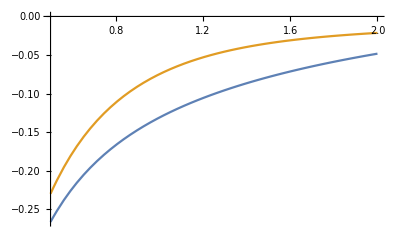

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[{20,11,3},α],Log[Zα]-logSymmetric3NoDiag[{20,11,3},α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->0.5}
```

-1.45982

```mathematica
Log[Zα]/.{α->5}
```

Log[693809375]

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,3}],{i,1,3}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,3}],{mat,Cases[allMats[[goodPos]],x_/;Total[Diagonal[x]]==20]}];
```

```mathematica
ZαDiag/.{α->1}
```

3

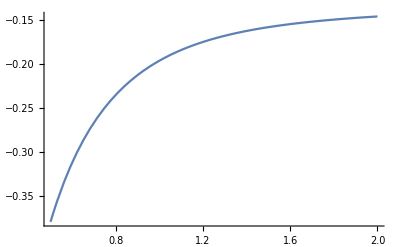

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[{20,11,3},20,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

1.09861

```mathematica
ZαDiag/.{α->5}//N//Log
```

18.4677

1.09861, 18.4677

#### Case 2

```mathematica
tk= {3,3,3,3,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

16

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

3108105

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

3108105

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

1828

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

1828

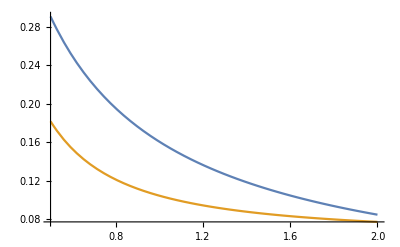

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

7.51098

```mathematica
Log[Zα]/.{α->5}//N
```

19.8828

7.51098, 19.8828

```mathematica
diagonalSum=10;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

16

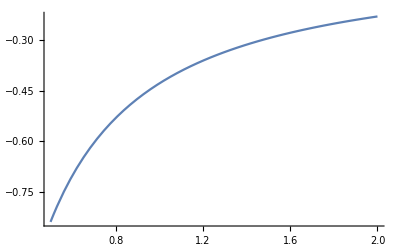

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

2.77259

```mathematica
ZαDiag/.{α->5}//N//Log
```

15.6481

2.77259, 15.6481

#### Case 3

```mathematica
tk= {2,2,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

8

4

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

715

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

715

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

17

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,Length[matsWithMargin[[1]]]}],{i,1,Length[matsWithMargin[[1]]]}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,Length[matsWithMargin[[1]]]}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

17

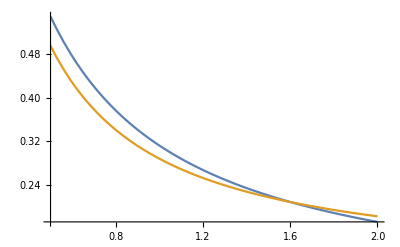

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

2.83321

```mathematica
Log[Zα]/.{α->5}//N
```

8.97778

```mathematica
diagonalSum=4;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,Length[matsWithMargin[[1]]]}],{i,1,Length[matsWithMargin[[1]]]}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,Length[matsWithMargin[[1]]]}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

6

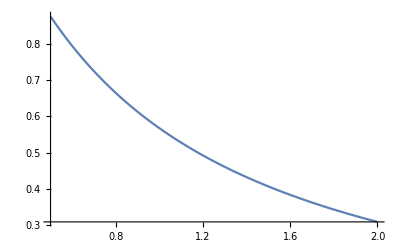

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

1.79176

```mathematica
ZαDiag/.{α->5}//N//Log
```

7.71869

1.79176, 7.71869

This is a tricky casae, there are diagonal sums where there is not a valid matrix although it is iwthin the hard support range. Need to detect this.

#### Case 4

```mathematica
tk= {2,2,2,2,2,2};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

12

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

230230

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

230230

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

388

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

388

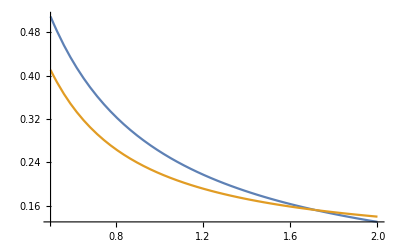

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

5.96101

```mathematica
Log[Zα]/.{α->5}//N
```

15.3585

5.96101, 15.3585

```mathematica
diagonalSum=6;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

20

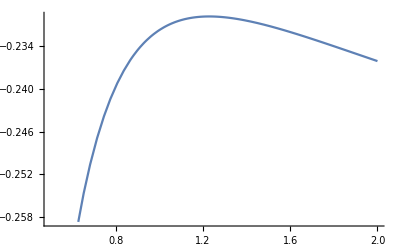

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

```mathematica
ZαDiag/.{α->1}//N//Log
```

2.99573

```mathematica
ZαDiag/.{α->5}//N//Log
```

12.6524

2.99573, 12.6524

```mathematica
Exp[Table[logSymmetric2Diag[tk,2*mIn,1]//N,{mIn,0,Total[tk]/2}][[{1,2,3,4,5,7}]]]//Total
```

387.046

```mathematica
logSymmetric2Diag[tk,12,1]//N
```

-3.82717

#### Loading matrices found by SIS

```mathematica
SISmatsRaw="0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 1 0 1 0 0 

0 0 1 1 0 0 
0 0 0 0 2 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 2 0 0 0 0 
0 0 1 1 0 0 

0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 0 1 1 0 
0 0 1 1 0 0 
0 1 0 0 1 0 
1 1 0 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 1 0 0 1 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 0 0 1 0 1 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

0 0 0 1 0 1 
0 0 1 0 0 1 
0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 

0 0 0 0 0 2 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 0 0 1 0 1 
0 0 0 1 1 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 0 0 0 2 
0 0 1 0 1 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
2 0 0 0 0 0 

0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
1 0 1 0 0 0 
1 0 1 0 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 1 0 1 
0 0 0 0 2 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 2 0 0 0 0 
1 0 1 0 0 0 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 0 2 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 0 1 1 0 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 0 0 2 
0 1 0 0 1 0 
0 1 0 1 0 0 
0 0 2 0 0 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 1 0 1 0 0 

0 0 1 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 1 1 0 0 
0 0 0 1 0 1 
1 0 0 0 1 0 
1 1 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 0 1 1 0 0 
0 0 0 1 0 1 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

0 0 0 0 1 1 
0 0 0 1 1 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
1 1 0 0 0 0 
1 0 1 0 0 0 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 1 1 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 1 0 1 
0 1 1 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 1 0 1 
0 0 0 1 0 1 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 0 0 2 
1 0 1 0 0 0 
0 0 0 2 0 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 0 0 1 1 0 
1 0 0 0 0 1 
0 1 0 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 0 2 0 
0 1 0 0 0 1 
0 0 2 0 0 0 
0 1 0 1 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 1 1 0 
0 0 1 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 1 0 0 1 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 2 0 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 1 1 0 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 0 2 0 
0 1 0 0 0 1 
0 0 2 0 0 0 
1 0 0 1 0 0 

0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 

0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
1 0 1 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 1 0 0 0 
0 1 0 1 0 0 

0 0 1 0 0 1 
0 0 0 1 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 0 0 1 1 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 1 0 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 1 1 0 0 0 

0 0 0 0 2 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 1 0 1 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 0 0 1 1 
0 2 0 0 0 0 
1 0 1 0 0 0 
1 0 1 0 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 0 1 0 0 0 

0 0 0 0 2 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 0 1 1 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 1 0 1 0 0 

0 0 0 0 0 2 
0 0 0 1 1 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 1 1 0 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

0 0 1 0 1 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 1 0 1 0 0 

0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 0 1 0 
1 0 0 0 0 1 
0 1 1 0 0 0 
1 0 0 1 0 0 

0 0 0 0 2 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 1 1 0 0 0 

0 0 2 0 0 0 
0 0 0 1 1 0 
2 0 0 0 0 0 
0 1 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 1 0 1 0 
0 0 0 0 0 2 
1 0 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 2 0 0 0 0 

0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 2 0 0 0 0 
1 0 1 0 0 0 

0 0 0 1 1 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
2 0 0 0 0 0 
0 0 1 1 0 0 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 0 0 0 1 1 
0 0 1 0 1 0 
0 1 0 0 0 1 
0 0 0 2 0 0 
1 1 0 0 0 0 
1 0 1 0 0 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 0 0 1 1 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
1 1 0 0 0 0 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 1 1 0 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
1 0 1 0 0 0 
0 0 0 2 0 0 

0 0 1 0 1 0 
0 0 0 1 1 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
1 1 0 0 0 0 
0 0 1 1 0 0 

0 0 0 2 0 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 1 0 1 0 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 1 0 1 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

0 0 0 1 1 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 2 0 0 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 0 1 1 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 1 1 0 0 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 0 1 0 0 1 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 1 0 0 0 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
0 1 1 0 0 0 
0 0 1 1 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 1 0 1 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

0 0 0 1 1 0 
0 0 0 0 0 2 
0 0 0 1 1 0 
1 0 1 0 0 0 
1 0 1 0 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 1 1 0 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 0 2 0 0 0 

0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 

0 0 1 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 1 1 0 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 0 2 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
1 0 0 1 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 0 1 1 0 
0 0 0 1 0 1 
0 0 0 0 1 1 
1 1 0 0 0 0 
1 0 1 0 0 0 
0 1 1 0 0 0 

0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 0 1 
1 0 1 0 0 0 
1 0 0 1 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 0 1 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
0 0 0 2 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 

0 0 0 1 1 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 1 1 0 0 0 

0 0 0 0 2 0 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
1 1 0 0 0 0 
1 0 0 1 0 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
1 0 0 1 0 0 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
2 0 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 0 0 2 0 0 
0 0 1 0 1 0 
0 1 0 0 1 0 
2 0 0 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 0 0 1 1 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 1 1 0 0 0 
1 1 0 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 0 1 0 1 
0 0 1 1 0 0 
0 1 0 0 1 0 
1 1 0 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 1 0 0 1 
0 0 0 0 1 1 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
1 1 0 0 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
1 0 0 1 0 0 

0 0 0 1 1 0 
0 0 0 1 1 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
1 0 0 1 0 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 1 1 0 
1 0 1 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 0 0 1 1 
0 0 1 0 0 1 
0 1 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 0 1 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 

0 0 0 1 1 0 
0 0 0 0 1 1 
0 0 2 0 0 0 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 1 0 1 0 0 

0 1 0 0 1 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 1 1 0 0 

0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 

0 0 0 1 0 1 
0 0 1 0 0 1 
0 1 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
1 0 0 1 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
1 0 1 0 0 0 
1 0 0 1 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
1 0 0 1 0 0 
0 0 1 1 0 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 0 1 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
1 1 0 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 0 0 1 0 1 
1 0 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 

0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 

0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 
1 0 0 1 0 0 
1 0 1 0 0 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 1 1 0 
1 0 1 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
1 1 0 0 0 0 
1 0 0 1 0 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
1 0 0 1 0 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
1 0 0 0 0 1 
1 0 1 0 0 0 
0 0 1 1 0 0 

0 0 1 0 1 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 0 2 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 0 1 1 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 1 0 0 1 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 1 1 0 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 2 0 0 0 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 0 1 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
1 0 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 1 1 0 0 0 
1 0 1 0 0 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

0 0 1 0 1 0 
0 2 0 0 0 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
1 0 0 0 0 1 
0 0 0 1 1 0 

0 0 1 1 0 0 
0 0 0 1 1 0 
1 0 0 0 1 0 
1 1 0 0 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 1 0 
0 0 0 0 0 2 
0 1 1 0 0 0 
0 0 0 2 0 0 

0 0 1 0 0 1 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 0 1 0 0 1 
0 0 1 1 0 0 
1 1 0 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 2 0 0 

0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 1 0 
1 0 0 1 0 0 
1 1 0 0 0 0 

0 0 0 1 0 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 0 1 1 0 0 

0 0 1 0 1 0 
0 0 1 0 1 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 0 0 1 1 
0 1 0 0 1 0 
0 0 1 1 0 0 
0 1 1 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 0 0 2 0 0 
1 0 0 0 1 0 
0 2 0 0 0 0 
0 0 1 0 0 1 
1 0 0 0 1 0 

0 0 0 0 0 2 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 1 0 1 0 0 
2 0 0 0 0 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 

0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 0 0 1 
1 0 0 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 0 1 0 1 0 
0 0 0 2 0 0 
1 0 0 0 1 0 
0 2 0 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 0 1 0 0 0 

0 0 2 0 0 0 
0 0 0 1 0 1 
2 0 0 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 1 1 0 0 
0 0 0 0 0 2 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 0 0 1 1 
0 0 0 1 0 1 
0 0 0 1 1 0 
0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 1 0 1 
0 0 1 0 0 1 
0 2 0 0 0 0 
0 0 1 1 0 0 

0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 1 1 0 0 
0 0 0 1 1 0 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
1 0 0 0 0 1 
0 0 1 0 1 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 1 0 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 1 0 
0 0 1 0 0 1 
0 1 1 0 0 0 
1 0 0 1 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
0 1 1 0 0 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 1 0 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 2 0 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 0 0 1 1 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

0 0 0 0 2 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 0 1 
2 0 0 0 0 0 
0 1 0 1 0 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 

0 0 1 0 0 1 
0 0 1 0 0 1 
1 1 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 1 0 0 0 0 

0 1 1 0 0 0 
1 0 1 0 0 0 
1 1 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 0 0 1 0 1 
1 0 0 1 0 0 
0 1 1 0 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 1 0 0 0 1 
1 0 0 0 1 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 0 1 0 
0 1 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 

0 0 1 0 0 1 
0 0 0 0 2 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 0 1 1 
0 1 0 0 1 0 
0 0 1 1 0 0 
1 0 1 0 0 0 

0 0 0 0 1 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 2 0 0 

0 0 1 1 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 1 0 0 1 0 

0 0 0 0 2 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 0 0 0 2 0 
1 0 0 1 0 0 
1 0 1 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 2 0 0 0 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 0 0 0 1 1 
0 1 0 1 0 0 
0 1 0 1 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 0 1 0 
0 0 0 2 0 0 
0 1 1 0 0 0 
0 0 0 0 0 2 

0 0 0 0 2 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 2 0 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 1 0 0 
0 0 1 0 0 1 
0 0 0 0 2 0 
0 1 0 1 0 0 

0 0 0 0 0 2 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
2 0 0 0 0 0 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 0 1 1 
0 1 0 0 0 1 
1 0 1 0 0 0 
0 0 1 1 0 0 

0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 1 1 0 0 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 0 0 1 1 
0 1 0 0 0 1 
0 1 1 0 0 0 
0 0 1 1 0 0 

0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 1 1 0 0 0 

0 0 0 1 0 1 
0 2 0 0 0 0 
0 0 0 0 1 1 
1 0 0 0 1 0 
0 0 1 1 0 0 
1 0 1 0 0 0 

0 0 0 2 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
2 0 0 0 0 0 
0 1 1 0 0 0 
0 1 1 0 0 0 

0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 1 0 0 0 1 
1 0 0 1 0 0 
0 0 0 1 0 1 
0 1 1 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 1 1 0 0 
0 2 0 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

0 0 0 0 1 1 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
1 0 0 1 0 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 
0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 1 1 0 0 
0 1 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
2 0 0 0 0 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
0 0 0 2 0 0 
1 0 1 0 0 0 
0 1 1 0 0 0 

0 0 0 0 2 0 
0 0 0 1 0 1 
0 0 0 1 0 1 
0 1 1 0 0 0 
2 0 0 0 0 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 

0 0 0 1 1 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
1 1 0 0 0 0 
0 0 1 1 0 0 

0 0 0 2 0 0 
0 0 1 0 1 0 
0 1 0 0 0 1 
2 0 0 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 0 0 1 1 
1 1 0 0 0 0 
0 0 1 0 0 1 
0 0 1 0 1 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 1 0 
0 1 0 0 1 0 
0 0 1 1 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 1 1 0 0 
0 1 0 0 0 1 
1 1 0 0 0 0 
0 0 0 0 2 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 1 0 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 1 0 0 

0 1 0 0 0 1 
1 0 0 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 1 0 1 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 1 1 0 0 
0 0 1 1 0 0 

0 0 0 1 0 1 
0 0 0 0 2 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 2 0 0 0 0 
1 0 0 1 0 0 

0 0 2 0 0 0 
0 0 0 0 0 2 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 2 0 0 0 0 

0 1 0 1 0 0 
1 0 0 0 0 1 
0 0 0 0 1 1 
1 0 0 0 1 0 
0 0 1 1 0 0 
0 1 1 0 0 0 

0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 

0 1 0 1 0 0 
1 0 1 0 0 0 
0 1 0 0 0 1 
1 0 0 0 0 1 
0 0 0 0 2 0 
0 0 1 1 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 0 0 1 0 
1 0 0 0 0 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

0 1 0 0 1 0 
1 0 0 1 0 0 
0 0 0 1 1 0 
0 1 1 0 0 0 
1 0 1 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 1 1 0 0 0 

2 0 0 0 0 0 
0 0 0 1 1 0 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 1 1 0 0 0 
1 0 0 1 0 0 
1 0 0 0 1 0 
0 1 0 0 0 1 
0 0 1 0 0 1 
0 0 0 1 1 0 

0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 0 0 1 1 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 1 0 
0 0 0 1 1 0 
1 0 0 1 0 0 
0 1 1 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

0 0 1 1 0 0 
0 0 0 0 1 1 
1 0 0 0 1 0 
1 0 0 0 0 1 
0 1 1 0 0 0 
0 1 0 1 0 0 

0 1 0 1 0 0 
1 0 0 1 0 0 
0 0 0 0 2 0 
1 1 0 0 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 0 1 0 
0 1 0 0 0 1 
1 0 1 0 0 0 
0 1 0 1 0 0 

0 0 0 1 1 0 
0 0 0 1 1 0 
0 0 2 0 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 0 1 0 1 0 
0 1 0 1 0 0 
0 0 1 0 1 0 
0 1 0 1 0 0 
2 0 0 0 0 0 

0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 
2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 

0 0 0 1 0 1 
0 0 0 1 0 1 
0 0 0 0 2 0 
1 1 0 0 0 0 
0 0 2 0 0 0 
1 1 0 0 0 0 

0 0 1 0 1 0 
0 0 0 1 0 1 
1 0 0 1 0 0 
0 1 1 0 0 0 
1 0 0 0 0 1 
0 1 0 0 1 0 

0 0 0 0 1 1 
0 2 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 0 0 2 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 0 2 0 0 0 

0 1 1 0 0 0 
1 0 0 0 1 0 
1 0 0 1 0 0 
0 0 1 0 0 1 
0 1 0 0 0 1 
0 0 0 1 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 0 1 0 1 
1 0 1 0 0 0 
0 1 0 0 0 1 
0 0 1 0 1 0 

0 1 0 1 0 0 
1 0 0 0 1 0 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 1 0 1 0 0 
0 0 0 0 0 2 

0 0 0 0 1 1 
0 0 1 1 0 0 
0 1 0 1 0 0 
0 1 1 0 0 0 
1 0 0 0 0 1 
1 0 0 0 1 0 

0 0 0 1 0 1 
0 0 0 0 1 1 
0 0 2 0 0 0 
1 0 0 0 1 0 
0 1 0 1 0 0 
1 1 0 0 0 0 

2 0 0 0 0 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 2 0 0 0 
0 1 0 0 1 0 
0 0 0 1 0 1 
0 1 0 0 1 0 

0 0 0 1 0 1 
0 0 0 1 1 0 
0 0 0 0 1 1 
1 1 0 0 0 0 
0 1 1 0 0 0 
1 0 1 0 0 0 

2 0 0 0 0 0 
0 0 0 0 0 2 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 2 0 0 0 0 

0 0 1 1 0 0 
0 0 1 1 0 0 
1 1 0 0 0 0 
1 1 0 0 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

0 0 1 0 0 1 
0 0 0 1 1 0 
1 0 0 0 1 0 
0 1 0 0 0 1 
0 1 1 0 0 0 
1 0 0 1 0 0 

0 2 0 0 0 0 
2 0 0 0 0 0 
0 0 0 1 0 1 
0 0 1 0 1 0 
0 0 0 1 0 1 
0 0 1 0 1 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 2 0 
0 0 0 2 0 0 
0 0 2 0 0 0 
0 0 0 0 0 2 

0 0 0 0 0 2 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 2 0 
2 0 0 0 0 0 

0 0 0 0 2 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
2 0 0 0 0 0 
0 0 0 0 0 2 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 0 0 0 0 2 
0 0 0 0 2 0 

2 0 0 0 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2 
0 0 0 2 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 

2 0 0 0 0 0 
0 0 0 0 2 0 
0 0 2 0 0 0 
0 0 0 2 0 0 
0 2 0 0 0 0 
0 0 0 0 0 2";
```

#### Analysis

```mathematica
SISmatsRaw1=ToExpression[StringSplit[StringSplit[SISmatsRaw,"\n"]," "]];
```

```mathematica
SISmats=Table[SISmatsRaw1[[7*(i-1)+1;;7*(i-1)+6]],{i,1,Length[SISmatsRaw1]/7+1}];
```

```mathematica
SISmats//Length
```

387

```mathematica
matsWithMargin//Length
```

388

Finding the examples of matrices which are not being generated by the sampler

There are examples of cases where there is a

```mathematica
Total[Diagonal[#]]&/@SISmats//Tally
```

{{4,90},{2,108},{6,20},{0,130},{8,15},{12,1}}

```mathematica
notFoundMatrices=Complement[matsWithMargin,SISmats];
```

```mathematica
Diagonal/@notFoundMatrices
```

{{2,2,2,2,2,2}}

```mathematica
MatrixForm/@notFoundMatrices
```

{(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2)}

Found (m_in = 1):

```mathematica
MatrixForm/@Cases[SISmats,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2]
```

{(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 2 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0)}

Not found:

```mathematica
MatrixForm/@Cases[notFoundMatrices,x_/;x[[1,1]]==2]
```

{(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0),(2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0)}

Computing the true marginal probabilities in this case

```mathematica
Cases[matsWithMargin,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2]//Length
```

22

```mathematica
Cases[matsWithMargin,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2][[;;,3,2]]
```

{2,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0}

So this probability should be 1/22..

```mathematica
marginPieces=Cases[matsWithMargin,x_/;x[[1,1]]==2&&Total[Diagonal[x]]==2][[;;,3;;,2]];
```

So, we need to count over the possible

```mathematica
Tally[marginPieces]
```

{{{2,0,0,0},1},{{1,1,0,0},3},{{1,0,1,0},3},{{1,0,0,1},3},{{0,2,0,0},1},{{0,1,1,0},3},{{0,1,0,1},3},{{0,0,2,0},1},{{0,0,1,1},3},{{0,0,0,2},1}}

```mathematica
logSymmetric2Diag[{2,2,2,2}-{1,0,1,0},0,1.00001]//Re
```

1.10466

```mathematica
logSymmetric2Diag[{2,2,2,2}-{2,0,0,0},0,1.00001]//Re
```

0.293729

#### Checking the off-diagonal counts

Hopefully this has been implemented correctly, so that we can now try to reproduce this in the c++ code

```mathematica
diagonalSum=2;
```

```mathematica
tmOut=(Total[tk]-diagonalSum)/2;
```

```mathematica
tmIn=diagonalSum/2;
```

```mathematica
tn=Length[tk];
```

```mathematica
αSymmetric2Diag[2*tmOut,Length[diagonalSum],0,1+0.00001]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
ths = Table[Module[{di,binom,α},di=sThis-sPrev;α=αSymmetric2Diag[2*tmOut,Length[diagonalSum],0,1]+0.00001;binom=Binomial[tk[[i]]-2 di+α-1,α-1];binom*If[(i==1&&sPrev!=0)||(i==tn&&sThis!=tmIn),0,1]*If[0<=tk[[i]]-2 di<=tmOut&&di>=0,1,0]],{i,1,tn},{sPrev,0,tmOut},{sThis,0,tmOut}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

```mathematica
tgs=Table[ths[[i,sPrev+1,sThis+1]]If[i==tn,1,Sum[ths[[i+1,sThis+1,sNext+1]],{sNext,0,tmOut}]],{i,1,tn},{sPrev,0,tmOut},{sThis,0,tmOut}]
```

{{{-5199462,-7807,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{60660390,288859,0,0,0},{0,60660390,288859,0,0},{0,0,60660390,287490,0},{0,0,0,60372900,0},{0,0,0,0,0}},{{0,-7770,-24642,0,0},{0,0,-5174820,-2443665,0},{0,0,0,-513169650,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,1,0},{0,0,0,666,0},{0,0,0,66045,0},{0,0,0,0,0}}}

Computing the transition probabilities P(s_i|s_{i-1})

```mathematica
tps=Table[tgs[[i,sPrev+1,sThis+1]]/Module[{s},s=Sum[tgs[[i,sPrev+1,t+1]],{t,0,tmOut}];If[s==0,1,s]],{i,1,tn},{sPrev,0,tmOut},{sThis,0,tmOut}]
```

{{{666/667,1/667,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{210/211,1/211,0,0,0},{0,210/211,1/211,0,0},{0,0,211/212,1/212,0},{0,0,0,1,0},{0,0,0,0,0}},{{0,35/146,111/146,0,0},{0,0,36/53,17/53,0},{0,0,0,1,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,1,0},{0,0,0,1,0},{0,0,0,1,0},{0,0,0,0,0}}}

```mathematica
tps[[-2]]//MatrixForm//N
```

(0. | 0.239726 | 0.760274 | 0. | 0.
0. | 0. | 0.679245 | 0.320755 | 0.
0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

Sample from these transitions

```mathematica
tRandS={};tp=1;
Module[{sNext},sNext=RandomChoice[tps[[1,0+1]]->Table[s,{s,0,tmOut}]];AppendTo[tRandS,sNext];tp*=tps[[1,0+1,sNext+1]];Do[sNext=RandomChoice[tps[[i,tRandS[[-1]]+1]]->Table[s,{s,0,tmOut}]];tp*=tps[[i,tRandS[[-1]]+1,sNext+1]];AppendTo[tRandS,sNext];,{i,2,tn}]]
{tRandS,tp}
```

{{0,0,1,3},2447550/10273801}

#### Case 5

```mathematica
tk= {2,2,1,1,1,1};
```

```mathematica
tT = Total[tk]
tn = Length[tk]
```

8

6

Uniform distribution over all of the matrices with the correct sum:

In order to do this, we need the total number of symmetric matrices to be a reasonable number:

```mathematica
Binomial[tT/2+tn(tn+1)/2-1,tn(tn+1)/2-1]
```

10626

We first generate flattened versions

```mathematica
allFlats=DeleteDuplicates[Flatten[Permutations/@IntegerPartitions[tT/2+tn(tn+1)/2,{tn(tn+1)/2}]-1,1]];
allFlats//Length
```

10626

Which we can then package into symmetric matrices:

```mathematica
conFlatToMat[vec_]:=Module[{q,res,t},q =1/2 (-1+√(1+8 Length[vec]));t=1;res=ConstantArray[0,{q,q}];Do[Do[res[[i,j]]+=vec[[t]];res[[j,i]]+=vec[[t]];t+=1,{j,i,q}],{i,1,q}];res]
```

```mathematica
allMats=Monitor[Table[conFlatToMat[allFlats[[ii]]],{ii,1,Length[allFlats]}],{ii}];
```

```mathematica
allMargins = Total[#]&/@allMats;
```

```mathematica
goodPos = Position[allMargins,tk][[;;,1]];
```

```mathematica
Length[goodPos]
```

36

```mathematica
matsWithMargin=allMats[[goodPos]];
```

Compute some correlators

```mathematica
Zα=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMargin}];
```

```mathematica
Zα/.{α->1}
```

36

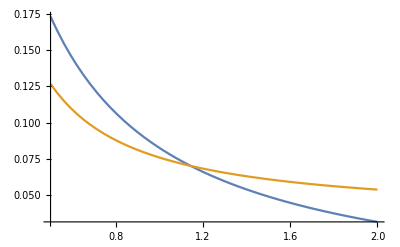

```mathematica
Plot[{Log[Zα]-logSymmetric2NoDiag[tk,α],Log[Zα]-logSymmetric3NoDiag[tk,α]},{α,0.5,2}]
```

```mathematica
Log[Zα]/.{α->1}//N
```

3.58352

```mathematica
Log[Zα]/.{α->5}//N
```

9.98737

2.70805, 7.53636

```mathematica
diagonalSum=6;
```

```mathematica
matsWithMarginDiag = Cases[matsWithMargin,x_/;Total[Diagonal[x]]==diagonalSum];
```

```mathematica
ZαDiag=Sum[Times@@Flatten[Table[Table[Binomial[mat[[i,j]]+α-1,α-1],{j,i+1,6}],{i,1,6}]]*Times@@Table[Binomial[mat[[i,i]]/2+α-1,α-1],{i,1,6}],{mat,matsWithMarginDiag}];
```

```mathematica
ZαDiag/.{α->1}
```

0

```mathematica
Log[388]//N
```

5.96101

```mathematica
Plot[{Log[ZαDiag]-logSymmetric2Diag[tk,diagonalSum,α]},{α,0.5,2}]
```

-Graphics-

```mathematica
ZαDiag/.{α->1}//N//Log
```

Indeterminate

```mathematica
ZαDiag/.{α->5}//N//Log
```

Indeterminate

2.99573, 12.6524

### count_asymmetric_matrix

### count_binary_matrix

```mathematica
tk={3,3,2,2,2,2};
tT = Total[tk]
tn = Length[tk]
```

14

6

```mathematica
allMats=conFlatToMat0Diag/@genAll01Vectors[tT/2,tn*(tn-1)/2];
allMats//Length
```

6435

```mathematica
allMatsWithMargin=Cases[allMats,x_/;Total[x]==tk];
allMatsWithMargin//Length
```

54

Check the shortest path length across these cases:

```mathematica
GraphDistance[AdjacencyGraph[#],1,2]&/@allMatsWithMargin//Mean//N
```

1.22222

## Moment matching validation

### alpha_symmetric_2

#### diagonal_sum = None

```mathematica
αSymmetric2NoDiag[T_,n_,α_]:= (T+(1+n) (-2+n (-1+T)+T) α)/(2 (-1+T)+n (-2+T+α+n α))
```

```mathematica
αSymmetric2NoDiag[200,10,1]//N
```

9.75402

```mathematica
αSymmetric2NoDiag[200,10,5]//N
```

41.168

#### diagonal_sum

```mathematica
αSymmetric2Diag[T_,Td_,n_,α_]:=-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))
```

```mathematica
αSymmetric2Diag[200,100,10,1]//N
```

3.6041

```mathematica
αSymmetric2Diag[200,100,10,5]//N
```

13.1526

### alpha_symmetric_3

#### diagonal_sum = None

```mathematica
αSymmetric3NoDiag[T_,n_,α_]:={(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}
```

```mathematica
αSymmetric3NoDiag[200,10,1]//N
```

{13.7998,7.53246}

```mathematica
αSymmetric3NoDiag[200,10,5]//N
```

{63.6326,30.4128}

#### diagonal_sum

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_3

#### diagonal_sum = None

#### diagonal_sum

## Sequential Importance Sampling

### Symmetric

```mathematica
validMin[ks_]:=Module[{m},m=Total[ks]/2;Flatten[Table[If[Total[Ceiling[(ks-(m-mIn))/2]]<=mIn,mIn,{}],{mIn,0,m}]]]
```

#### sample_diagonal_sum

Possible m_in (note that this is not necessarily a continuous range):

```mathematica
tk = {2,2,2,2};
```

```mathematica
tk = {3,3,3,3,2,2};
```

```mathematica
validMin[tk,Total[tk]/2]
```

{0,1,2,3,4,5,6,7}

Adding some to the alpha to avoid divergences

```mathematica
Table[αSymmetric2Diag[Total[tk],2*mIn,Length[tk],1+0.0000001],{mIn,validMin[tk]}]
```

{16.5,11.598,6.79851,4.07576,2.60013,1.75377,1.23473,0.897163}

```mathematica
diagValProbs = Table[Re[logSymmetric2Diag[tk,2*mIn,1+0.0000001]],{mIn,validMin[tk]}]//Exp
```

{324.742,619.863,538.022,281.498,99.2114,24.5501,4.20982,0.459237}

Associated entropy:

```mathematica
tDiagSum=7;
```

```mathematica
-Log[diagValProbs[[tDiagSum+1]]/Total[diagValProbs]]
```

8.32387

Note that some of these cases have negative alpha values... That’s a bit problematic but should be ok for the SIS

#### sample_diagonal_entries

#### sample_off_diagonal_table

### Asymmetric

### Symmetric binary matrices

Since the Erdos-Gallai condition does not (as far as I can tell) factor nicely as the estimate does. Therefore we must adopt an alternative strategy.

```mathematica
erdosGallaiCondition[ks_]:=Module[{ksSorted,n},n=Length[ks];ksSorted=Reverse[Sort[ks]];And@@Table[Sum[ksSorted[[i]],{i,1,l}]<=l(l-1)+Sum[Min[ksSorted[[i]],l],{i,l+1,n}],{l,1,n}]]
```

```mathematica
tk={5,3,3,2,2,1,1};
```

```mathematica
erdosGallaiCondition[tk]
```

True

```mathematica
erdosGallaiCondition[{5,1,2,9,14,9,11,3,1,9,3,2,5,14,5,7}]
```

False

```mathematica
erdosGallaiCondition[{18,6,5,10,10,7,10,2,18,19,24,24,11,27,7,18,26,6,3,36,18,13,2,13,5,5,1,14,7,1,20,6,18,11,9,14,4,7,9,1,9,40,13,16,50,3,1,2,3,10,2,1,14,11,20,7,14,6,49,21,16,4,6,17}]
```

True

Trying to check how we can rapidly compute whether a local change will disrupt the Erdos-Gallai condition:

```mathematica
erdosGallaiConditionParts[ks_]:=Module[{ksSorted,n},n=Length[ks];ksSorted=Reverse[Sort[ks]];Table[{l(l-1)+Sum[Min[ksSorted[[i]],l],{i,l+1,n}],Sum[ksSorted[[i]],{i,1,l}]},{l,1,n}]]
```

```mathematica
tk={5,1,2,9,14,9,11,3,1,9,3,2,5,14,5,7};
```

```mathematica
2(2-1)+Sum[Min[Reverse[Sort[tk]][[i]],2],{i,2+1,Length[tk]}]
```

28

```mathematica
erdosGallaiConditionParts[tk]
```

{{15,14},{28,28},{39,39},{48,48},{57,57},{63,66},{69,73},{78,78},{89,83},{102,88},{119,91},{138,94},{160,96},{184,98},{211,99},{240,100}}

```mathematica
erdosGallaiConditionParts[{3,1,1,1}]
```

{0,0,2,6}

```mathematica
erdosGallaiCondition[{4,3,1,1,1}]
```

False

```mathematica
erdosGallaiConditionParts[{4,3,2,2,1}]
```

{0,0,0,2,8}

(c = 3, n = 5 → k[c] = 2, k[n] = 1)

g_l(a):

```mathematica
erdosGallaiConditionParts[{3,3,2,2,1}-{0,1,1,1,0}]
```

{1,0,2,6,12}

g_l(b):

```mathematica
erdosGallaiConditionParts[{3,3,2,2,1}-{0,1,0,1,1}]
```

{0,0,0,4,12}

```mathematica
erdosGallaiConditionParts[{3,3,2,2,1}-{0,1,0,1,1}]-erdosGallaiConditionParts[{3,3,2,2,1}-{0,1,1,1,0}]
```

{-1,0,-2,-2,0}

(c = 3, n = 6 → k[c] = 2, k[n] = 1)

g_l(a):

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}-{0,1,0,1,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0}]
```

{14,24,28,28,28,32,38,46,56,70,86,104,124,146,170,196,226,258,292,328}

g_l(b):

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}-{0,1,0,1,0,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0}]
```

{14,24,27,28,28,30,36,44,56,70,86,104,124,146,170,196,226,258,292,328}

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}-{0,1,0,1,0,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0}]-erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}-{0,1,0,1,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0}]
```

{0,0,-1,0,0,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}][[2;;]]-erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}[[2;;]]-{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}]
```

{10,6,6,6,6,6,6,6,6,6,6,8,10,12,14,16,18,20,22}

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}][[2;;]]
```

{24,30,32,32,34,38,44,54,66,80,96,116,138,162,188,218,250,284,320}

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}[[2;;]]]
```

{13,22,27,29,29,31,35,43,53,65,79,97,117,139,163,191,221,253,287}

```mathematica
erdosGallaiConditionParts[{5,5,5,5,4,4,4,4,3,3,3,3,2,2,2,2,1,1,1,1}[[2;;]]-{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}]
```

{14,24,26,26,28,32,38,48,60,74,90,108,128,150,174,202,232,264,298}

```mathematica
erdosGallaiConditionParts[{3,2,2,1,1,1}]
```

{2,2,2,6,12,20}

```mathematica
erdosGallaiConditionParts[{3,2,2,1,1,1}-{0,1,0,0,0,0}]
```

{2,1,3,7,13,21}

```mathematica
erdosGallaiConditionParts[{3, 2, 2, 1, 1, 0, 1}]
```

{2,2,2,6,12,20,32}

```mathematica
erdosGallaiConditionParts[{1, 2, 0, 0, 1}]
```

{0,0,2,8,16}

```mathematica
erdosGallaiConditionParts[ks_]:=Module[{ksSorted,n},n=Length[ks];ksSorted=Reverse[Sort[ks]];Table[{l(l-1),Sum[Min[ksSorted[[i]],l],{i,l+1,n}],Sum[ksSorted[[i]],{i,1,l}]},{l,1,n}]]
```

```mathematica
erdosGallaiConditionParts[{3, 2, 2, 1, 1, 0, 1}]
```

{{0,5,3},{2,5,5},{6,3,7},{12,2,8},{20,1,9},{30,0,10},{42,0,10}}

## Workspace

### alpha_symmetric_2

#### diagonal_sum = None

Convert to the c++ format

```mathematica
αSymmetric2NoDiag[2 m,n,α]
```

(2 m+(1+n) (-2+2 m+(-1+2 m) n) α)/(2 (-1+2 m)+n (-2+2 m+α+n α))

2nd central moments of the Dirichlet-Multinomial distribution with total t and length n, we want n → n(n+1)/2 here:

-Graphics-

```mathematica
secondCentralMoment = t/n(n α + t)/(n α + 1)(d - n^(-1));
```

In order to compute the covariances of the degrees this is going to be sum over a variety of contirbutions. We can split into two cases:

i = j:

```mathematica
1+2*(n - 1)+(n-1) + (n-1)(n-2)//Simplify
```

n^2

```mathematica
4*1*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1}) +2*2*(n - 1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})+(n-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1}) + (n-1)(n-2)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})//Simplify
```

((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))

```mathematica
(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}/.{αM->αSymmetric2NoDiag[T,n,1]}//FullSimplify)==(((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1})
```

((-1+n) (2+n) T (n+n^2+T))/(n^2 (1+n) (2+n+n^2))==((-2+n+n^2) T (n (1+n)+T))/(n^2 (1+n) (2+n+n^2))

```mathematica
Solve[(((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1})==secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM},αM]//FullSimplify
```

{{αM→(-n (3+n)+2 (-1+T)+n (2+n) T)/(2 (-1+T)+n (-1+n+T))}}

```mathematica
Solve[((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))==(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}),αM]//FullSimplify
```

{{αM→(T+(1+n) (-2+n (-1+T)+T) α)/(2 (-1+T)+n (-2+T+α+n α))}}

i != j:

```mathematica
1 + 1 + 2(n-1) + ((n-1)^2-1)//Simplify
```

n^2

```mathematica
1 *(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->1})+ 1 *(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})*4+ 2(n-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})*2 + ((n-1)^2-1)*(secondCentralMoment/.{t->T/2,n->n(n+1)/2,d->0})//Simplify
```

-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))

```mathematica
((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/(-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α)))//Simplify
```

1-n

```mathematica
αSymmetric2NoDiag[t,n,1]
```

```mathematica
-((2+n) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))/.{α->1}/.{T->34,n->3}
```

-1955/126

#### diagonal_sum

Convert to the c++ format

```mathematica
αSymmetric2Diag[2 m,2m mu, n,α]
```

-((4 m^2 mu^2 (-1+n) (2+(-1+n) n α)+4 m mu (-1+n) n α (2+(-1+n) n α)-4 m^2 (-1+n) (1+n α) (2+(-1+n) n α)+(2 m-2 m mu) (-2+n) (1+n α) (2 m-2 m mu+(-1+n) n α))/(n (4 m^2 mu^2 (-1+n) (2+(-1+n) n α)+4 m mu (-1+n) n α (2+(-1+n) n α)-2 m (-1+n) (1+n α) (2+(-1+n) n α)+(2 m-2 m mu) (-2+n) (1+n α) (2 m-2 m mu+(-1+n) n α))))

11:

```mathematica
1+2*(n - 1)+(n-1) + (n-1)(n-2)//Simplify
```

n^2

```mathematica
4*1*(secondCentralMoment/.{t->Td/2,n->n,d->1}) +2*2*(n - 1)*0+(n-1)*(secondCentralMoment/.{t->To/2,n->n(n-1)/2,d->1}) + (n-1)(n-2)*(secondCentralMoment/.{t->To/2,n->n(n-1)/2,d->0})//Simplify
```

(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2

```mathematica
(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2/.{α->1,n->3,To->14,Td->20}
```

295/9

```mathematica
αMrule=Solve[(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2==(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}),αM][[1]]//FullSimplify
```

{αM→-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) To (1+n α) (To+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) To (1+n α) (To+(-1+n) n α))))}

```mathematica
αM/.αMrule/.{To->T - Td}//Simplify
```

-(((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T^2 (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))/(n ((-1+n) Td^2 (2+(-1+n) n α)+2 (-1+n) n Td α (2+(-1+n) n α)-(-1+n) T (1+n α) (2+(-1+n) n α)+(-2+n) (T-Td) (1+n α) (T-Td+(-1+n) n α))))

22:

### alpha_symmetric_3

third moment of DM:

```mathematica
thirdCentralMoment = t/n(n α + t)(n α + 2 t)/((n α + 1)(n α + 2))(d3 - d2/n + 2/n^2);
```

#### diagonal_sum = None

111:

```mathematica
1+3(n-1)+3(n-1)+3(n-1)(n-2)+(n-1)(n-2)(n-3)+3(n-1)(n-2)+n-1//Simplify
```

n^3

```mathematica
1(thirdCentralMoment /.{d3->1,d2->3}/.{t->T/2,n->n(n+1)/2})*8+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*4+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*2+3(n-1)(n-2)(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*2+(n-1)(n-2)(n-3)*(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*1+3(n-1)(n-2)*(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*1+(n-1)*(thirdCentralMoment /.{d3->1,d2->3}/.{t->T/2,n->n(n+1)/2})*1//Simplify
```

((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))

```mathematica
((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))/.{α->1,T->34,n->3}
```

1955/27

```mathematica
1/2((thirdCentralMoment/.{d3->1,d2->3,t->T}/.{α->alphaMinus})+(thirdCentralMoment/.{d3->1,d2->3,t->T}/.{α->alphaPlus}))/.{T->34,n->3}//Simplify
```

1955/27

```mathematica
Solve[{((8-10 n+n^2+n^3) T (2 T^2+3 n (1+n) T α+n^2 (1+n)^2 α^2))/(n^3 (1+n) (2+n α+n^2 α) (4+n α+n^2 α))==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),((-2+n+n^2) T (T+n (1+n) α))/(n^2 (1+n) (2+n α+n^2 α))==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

{{αP→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),αM→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)},{αP→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)-√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3),αM→(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)}}

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)/.{α->1,T->200,n->10}//N
```

13.7998

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+√((-1+α+n α) (T-(1+n) α) (T+n (1+n) α) (-4-4 n+4 T+3 n T+n (1+n) (n (-1+T)+T) α) (4 (-1+T)+n (-4+5 T+(1+n) (-5+4 T+n (-4+5 T)) α+n (1+n)^2 (-2+n (-1+T)+T) α^2)))+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)/.{Sqrt[a_]->0}//FullSimplify
```

(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/(8 (1+n)^2-2 (1+n) (8+5 n) T+2 (4+n (5+2 n)) T^2+n (1+n) (2 n (1+2 n)-3 n (3+n) T+(4+n (3+n)) T^2-2 (1+T)) α+n^2 (1+n)^2 (-3+n (-5+T)+5 T) α^2+2 n^3 (1+n)^3 α^3)

```mathematica
denominator=
```

```mathematica
(T^2 (4+n+(1+n) (4+n (11+4 n)) α+n (1+n)^3 (2+n) α^2)+(1+n) T (-4+α (-12+n (-17-11 n-(1+n) (7+n (4+3 n)) α+n (1+n)^3 α^2)))+(1+n)^2 α (8+n (4+α (2+n (7+2 n-(1+n) (4+n) α)))))/.{T->200,n->10,α->1}
```

6820008328

#### diagonal_sum

111:

```mathematica
1+3(n-1)+3(n-1)+3(n-1)(n-2)+(n-1)(n-2)(n-3)+3(n-1)(n-2)+n-1//Simplify
```

n^3

```mathematica
1(thirdCentralMoment /.{d3->1,d2->3}/.{t->Td/2,n->n})*8+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*0+3(n-1)(thirdCentralMoment /.{d3->0,d2->1}/.{t->T/2,n->n(n+1)/2})*0+3(n-1)(n-2)(thirdCentralMoment /.{d3->0,d2->0}/.{t->T/2,n->n(n+1)/2})*0+(n-1)(n-2)(n-3)*(thirdCentralMoment /.{d3->0,d2->0}/.{t->To/2,n->n(n-1)/2})*1+3(n-1)(n-2)*(thirdCentralMoment /.{d3->0,d2->1}/.{t->To/2,n->n(n-1)/2})*1+(n-1)*(thirdCentralMoment /.{d3->1,d2->3}/.{t->To/2,n->n(n-1)/2})*1//Simplify
```

(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))

```mathematica
(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))/.{α->1,n->3,To->14,Td->20}
```

2273/27

```mathematica
Solve[{(8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),(((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

$Aborted

```mathematica
Solve[{((8 (-3+n) (-2+n) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)-6 (-2+n) (-4-n+n^2) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+(8+6 n-5 n^2-2 n^3+n^4) To (1+n α) (2+n α) (To+(-1+n) n α) (2 To+(-1+n) n α)+2 (-1+n)^2 (2-3 n+n^2) Td (Td+n α) (Td+2 n α) (2-n α+n^2 α) (4-n α+n^2 α))/(4 (-1+n)^2 n^3 (1+n α) (2+n α) (1+1/2 (-1+n) n α) (2+1/2 (-1+n) n α))/.{α->1})==1/2((thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αP})+(thirdCentralMoment/.{d3->1,d2->3}/.{t->T,n->n,α->αM})),((((-1+n) Td^2)/(1+n α)+(2 (-1+n) n Td α)/(1+n α)+((-2+n) To (To+(-1+n) n α))/(2-n α+n^2 α))/n^2/.{α->1})==1/2((secondCentralMoment/.{d->1}/.{t->T,n->n,α->αP})+(secondCentralMoment/.{d->1}/.{t->T,n->n,α->αM}))},{αP,αM}]//FullSimplify
```

$Aborted

### alpha_symmetric_block_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_symmetric_block_3

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_2

#### diagonal_sum = None

#### diagonal_sum

### alpha_asymmetric_3

#### diagonal_sum = None

#### diagonal_sum

## Workspace

Checking what the matching value of α is if we are considering the multinomial distribution α -> ∞

Limiting covariance:

```mathematica
Normal[Series[symmetricMultiDiagVariance/.{α->1/λ},{λ,0,0}]]
```

(2 (-2 m+m n+ms n))/n^2

Corresponding α for the moment matching:

What values of ms/m and α yield covariance structures that can be moment matched?

```mathematica
Solve[2m/n(n α + 2 m)/(n α + 1)(1-n^(-1))==v,α]
```

{{α→(4 m^2-4 m^2 n+n^2 v)/(n (-2 m+2 m n-n^2 v))}}

```mathematica
matchedα=(4 m^2-4 m^2 n+n^2 v)/(n (-2 m+2 m n-n^2 v))/.{v->symmetricMultiDiagVariance}//Simplify
```

(m (-2+n) (1+n α) (4 ms-(-1+n) n α)+2 m^2 n (1+(1-n+n^2) α+(-1+n)^2 n α^2)+ms (-((-1+n) n α (6-n+n^2 α))+ms (8+2 n (-3+α)+2 n^2 α-2 n^3 α)))/(n (2 m^2 (-2+n) (1+n α)-m (1+n α) (4 ms (-2+n)+(-1+n) (2+n α))+ms ((-1+n) n α (6-n+n^2 α)+2 ms (-4+3 n-n α-n^2 α+n^3 α))))

```mathematica
matchedα/.{ms->(1-μ) m}/.{m->100,n->10}/.{μ->0.1,α->1.}
```

1.18637

```mathematica
(4 m^2-4 m^2 n+n^2 v)/(n (-2 m+2 m n-n^2 v))/.{v->symmetricMultiAllDiagVariance}/.{m->100,n->10}/.{α->1}
```

6067/622

```mathematica
(-((1+n)*(2+n))+T*(2+n*(2+n)))/((-2+n)*(1+n)+T*(2+n))/.{T->2m}/.{m->100,n->10}
```

6067/622

It seems that only large mixing and high α will produce an invalid match (which we can probably comfortably send to α = ∞ to approximately match to ensure the estimate is well-behaved)

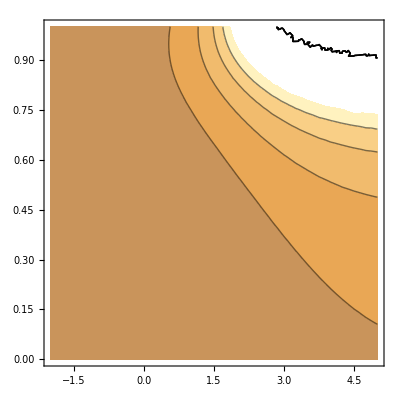

```mathematica
ContourPlot[matchedα/.{ms->(1-μ) m,α->Exp[lα]}/.{m->100,n->10},{lα,-2,5},{μ,0,1}]
```

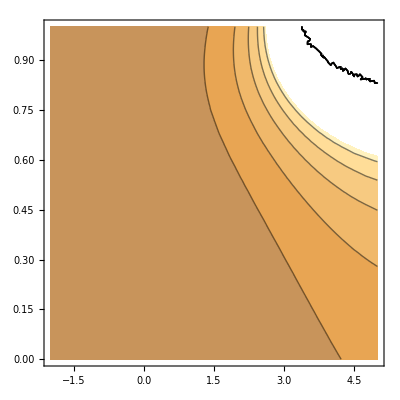

```mathematica
ContourPlot[matchedα/.{ms->(1-μ) m,α->Exp[lα]}/.{m->100,n->5},{lα,-2,5},{μ,0,1}]
```

```mathematica
matchedα/.{ms->(1-μ) m}/.{m->100,n->10}/.{α->10,μ->1}
```

7340/31

Should plot performance relative to the SIS results. Previously we had found that for very heterogeneous margins, and for